Hey look it’s this again, just for the infinite square well

```mathematica
Critical[consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Round[consts[[2]]];
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

Testing with parameters that are close to what we’ve used before:

```mathematica
Critical[{0.1,25000}]
```

{1.57912×10^-8,6.3165×10^-8,1.42121×10^-7,2.5266×10^-7,3.94781×10^-7,5.68485×10^-7,7.73771×10^-7,1.01064×10^-6,1.27909×10^-6,1.57912×10^-6,1.91074×10^-6,2.27394×10^-6,2.66872×10^-6,3.09508×10^-6,3.55303×10^-6,4.04256×10^-6,4.56367×10^-6,5.11636×10^-6,5.70064×10^-6,6.3165×10^-6,6.96394×10^-6,7.64296×10^-6,8.35357×10^-6,9.09575×10^-6,9.86953×10^-6}

Testing with a variety of Δρs. Lowest: 0.0125. Highest: 204.8.

```mathematica
ens=ParallelTable[Critical[{0.1*2^i,25000}],{i,-3,11}];
```

Eigenvalues::arh: Because finding 25 out of the 122 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

This creates a list of the E_ns at each value of Δρ. I normalized the energies by dividing them by the first calculated energy, so that they could be more easily compared (that is, each list starts with 1).

```mathematica
evslist=Table[{j,ens[[j,i]]/ens[[1,i]]},{i,1,25},{j,1,Length[ens]}];
```

Actual infinite square well energies, for a well of width 25000.

```mathematica
actualEs=Table[i^2 π^2 / (25000.)^2,{i,1,25}]
```

{1.57914×10^-8,6.31655×10^-8,1.42122×10^-7,2.52662×10^-7,3.94784×10^-7,5.68489×10^-7,7.73777×10^-7,1.01065×10^-6,1.2791×10^-6,1.57914×10^-6,1.91076×10^-6,2.27396×10^-6,2.66874×10^-6,3.09511×10^-6,3.55306×10^-6,4.04259×10^-6,4.56371×10^-6,5.1164×10^-6,5.70068×10^-6,6.31655×10^-6,6.96399×10^-6,7.64302×10^-6,8.35363×10^-6,9.09583×10^-6,9.8696×10^-6}

I normalized those the same way

```mathematica
actualEsratios=Table[actualEs[[i]]/ens[[1,i]],{i,1,25}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

Plot showing the divergence of the calculated energies from the actual value (and also, interestingly, each other.)

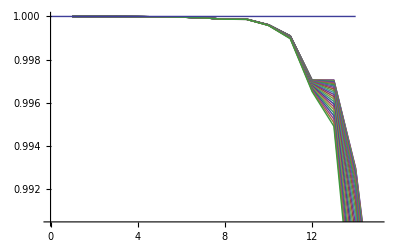

```mathematica
Show[ListPlot[evslist,Joined->True],Plot[1.,{x,0,14}]]
```

These plots have the actual difference in energies plotted at the value of Δρ where they were calculated.

```mathematica
Deltas=Table[{0.1*2^i,actualEs[[j]]-ens[[i+4,j]]},{i,-3,11},{j,0,25}];
```

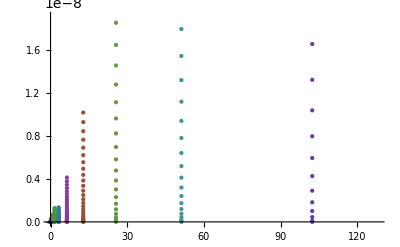

```mathematica
ListPlot[Deltas]
```

close in on the low range

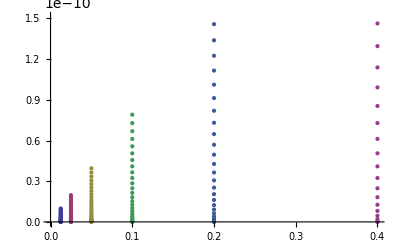

```mathematica
ListPlot[Deltas[[1;;6]]]
```